(x<0||x>1)&&(y≤0||y≥1)

And[Or[Less[x,0],Greater[x,1]],Or[LessEqual[y,0],GreaterEqual[y,1]]]

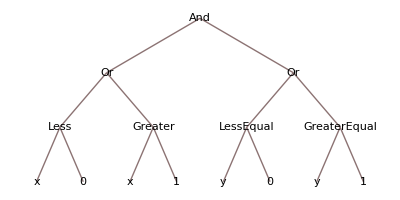

y≤0

```mathematica
e=(x<0 || x>1) && (y<=0 || y>=1)
FullForm[e]
TreeForm[e]
e[[2,1]]
```

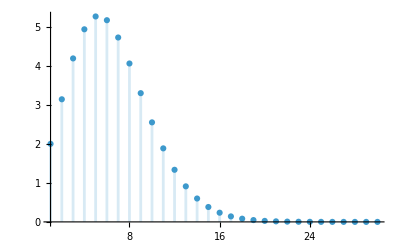

```mathematica
objemKoule[n_]:=(Pi^(n/2))/(Gamma[n/2+1]);
DiscretePlot[objemKoule[n],{n,1,30}]
```

```mathematica
"Max. pro n=5"
```

```mathematica
DiscreteLimit[(Pi^(n/2))/(Gamma[n/2+1]),n->Infinity]
```

0

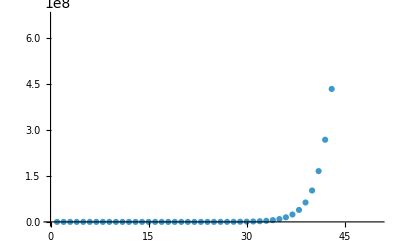

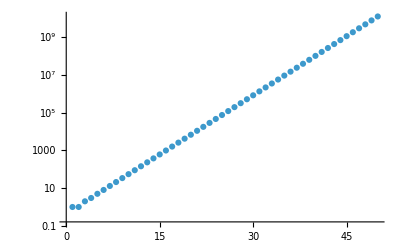

```mathematica
fib=Table[Fibonacci[n],{n,1,50}];
ListPlot[fib]
ListLogPlot[fib]
```

```mathematica
"Fibonacciho čísla rostou exponenciálně -> na log grafu tvoří přímku"
```

```mathematica
ClearAll[randomWalk,randomCisla]
randomCisla[n_ ]:=Table[RandomReal[{-1,1}],n]
randomWalk[n_, seznamRandom_]:=Table[Total[seznamRandom[[1;;i]]],{i,1,n}]
```

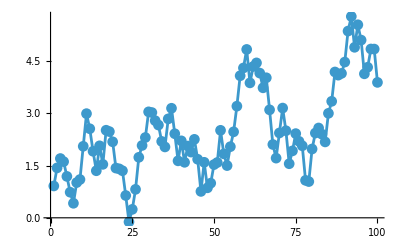

```mathematica
ListLinePlot[randomWalk[100,randomCisla[100]],PlotMarkers->Automatic]
```

```mathematica
Clear[randomWalk2D]
randomWalk2D[rw1_,rw2_]:=Transpose[Append[{rw1},rw2]]
```

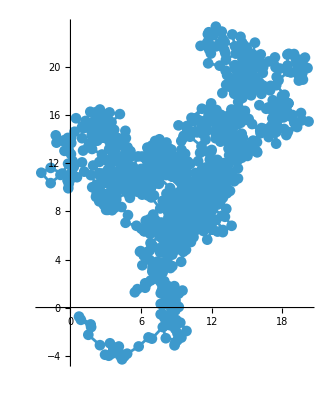

```mathematica
rw=randomWalk2D[randomWalk[1000,randomCisla[1000]],randomWalk[1000,randomCisla[1000]]];
ListLinePlot[rw,PlotMarkers->Automatic,AspectRatio->Automatic]
{a,b}={Min[rw],Max[rw]};Animate[ListLinePlot[rw[[1;;i]],PlotRange->{{a,b},{a,b}},AspectRatio->1],{i,1,Length[rw],1}]
```

```mathematica
seznamVektoru[n_]:=Transpose[Append[{randomCisla[n]},randomCisla[n]]]
odhadPi[n_]:=4/n*Count[seznamVektoru[n],r_/;Norm[r]<=1]
```

```mathematica
N[odhadPi[1000000]-Pi]
```

-0.00164465

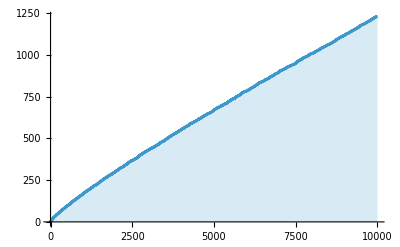

```mathematica
DiscretePlot[PrimePi[n],{n,1, 10000}]
```

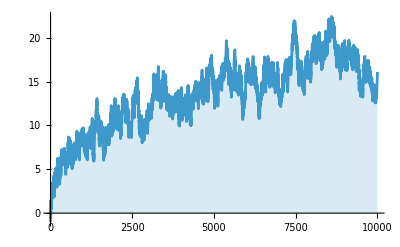

```mathematica
DiscretePlot[LogIntegral[n]-LogIntegral[2]-PrimePi[n],{n,2,10000}]
```

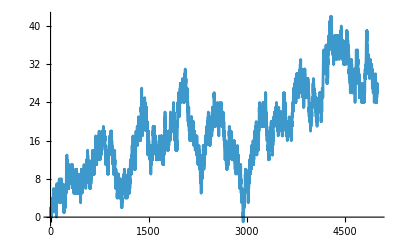

```mathematica
Clear[dPrime]
dPrime[n_]:=Accumulate[Mod[Prime[Range[n]],4]-2]
ListLinePlot[dPrime[5000]]
```

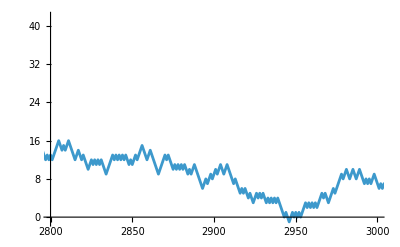

```mathematica
ListLinePlot[dPrime[5000],PlotRange->{{2800,3000},Automatic}]
```

```mathematica
"n_0 = 2946"
```